Wolfram Online Mini Campus. Part 8

Instagram Posts
Pinterest Posts
"Translation" of  SageMath Online Mini Campus. Part 8

Functions as Creativity Expressions

```mathematica
Manipulate[Graphics[Table[{Hue[(i+10*j)/100],PointSize[0.0001*i],
Point[{Cos[Pi*i/50]^3+j,j*Sin[Pi*i/50]/3}]},{i,100},{j,N}],
GridLines->Automatic,ImageSize->Large,Axes->True],{N,Range[1,5,1]}]
```

```mathematica
Print[CharacterRange["数","斀"]];CharacterRange["⚐","⚜"]
Print[FromCharacterCode[Range[8592,8647,1]]]; 
FromCharacterCode[Range[8648,8703,1]]
tf=Table[{n*Cos[n/4],n*Sin[n/4]},{n,8703-8591}];
mf=ToString /@ CharacterRange["←","⇿"];
ListPlot[List /@tf,PlotMarkers->mf,
PlotStyle->"DarkBands",ImageSize->700]
```

{数,敱,敲,敳,整,敵,敶,敷,數,敹,敺,敻,敼,敽,敾,敿,斀}

{⚐,⚑,⚒,⚓,⚔,⚕,⚖,⚗,⚘,⚙,⚚,⚛,⚜}

←↑→↓↔↕↖↗↘↙↚↛↜↝↞↟↠↡↢↣↤↥↦↧↨↩↪↫↬↭↮↯↰↱↲↳↴↵↶↷↸↹↺↻↼↽↾↿⇀⇁⇂⇃⇄⇅⇆⇇

⇈⇉⇊⇋⇌⇍⇎⇏⇐⇑⇒⇓⇔⇕⇖⇗⇘⇙⇚⇛⇜⇝⇞⇟⇠⇡⇢⇣⇤⇥⇦⇧⇨⇩⇪⇫⇬⇭⇮⇯⇰⇱⇲⇳⇴⇵⇶⇷⇸⇹⇺⇻⇼⇽⇾⇿

-Graphics-

```mathematica
ListLinePlot[Table[{Sin[2t],Cos[7 t]+Cos[t]},
{t,0,2 Pi,Pi/75}],Axes -> False,ImageSize->500]/.
Line[rest_]:>{Arrowheads[Table[.05,{i, 0, 1,.03}]],
Arrow[BSplineCurve@rest]}
```

-Graphics-

```mathematica
tpp=PolarPlot[Evaluate[Table[Cos[12t]+i,{i,3}]],{t,0,2Pi},
ColorFunction->Function[{x,y,t,r},ColorData["CandyColors"][r]],
RegionFunction->Function[{x,y,t,r},Cos[12t]<0.75]];
trp=ParametricPlot[Evaluate[Table[{(Cos[12t]/2+i)*Cos[t],
(Cos[12t/2]+i)*Sin[t]},{i,3}]],{t,0,2Pi},
ColorFunction->Function[{x,y,t},
ColorData["CandyColors"][Abs[Cos[12t]]]]];
Show[tpp,trp,Axes->False,ImageSize->500]
```

-Graphics-

```mathematica
cfbb=Function[{x,y,t,r},ColorData["BrightBands"][r]];
cfdb=Function[{x,y,t,r},ColorData["DarkBands"][r]];
pp1=PolarPlot[Exp[Cos[t]^2+Sin[t]]-3Cos[4t]+Sin[t/12],
{t, 0,6π},ColorFunction->cfbb];
pp2=PolarPlot[-Floor[t]*Sin[t]/2,{t,0,6Pi},
ExclusionsStyle->Dashed,ColorFunction->cfdb];
Show[pp1,pp2,Axes->False,PlotStyle->Thick,ImageSize->500]
```

-Graphics-

```mathematica
X1=(2+Cos[v/2]*Sin[u]-Sin[v/2]*Sin[5u])*Cos[v]; 
X2=6u Cos[v];
Y1=(2+Cos[v/3]*Sin[u]-Sin[v/2]*Sin[4u])*Sin[v]; 
Y2=6u Sin[v];
Z1=16Abs[Sin[v/2]*Sin[u]+Cos[v/2]*Sin[4u]]; 
Z2=4Im[(u Exp[I v]^5)^(1/5)];
tpp1=Table[ParametricPlot3D[{i*X1,i*Y1,Z1},
{u,0,2Pi},{v,0,2Pi},Mesh->None,
ColorFunction->"RoseColors",
PlotStyle->Opacity[0.5]],{i,3}];
tpp2=ParametricPlot3D[{X2,Y2,Z2},
{u,0,2},{v,0,2 Pi}, Mesh->None,
ExclusionsStyle->{None,Gray},
PlotStyle->Directive[Darker[Green],Opacity[0.7]]];     
Show[tpp1,tpp2,Axes->False,
Boxed->False,PlotPoints->20,ImageSize->700]
```

-Graphics3D-

```mathematica
Show[tpp1,tpp2,Axes->False,Boxed->False,ViewPoint->{0,3,5}]
```

-Graphics3D-

```mathematica
With[{f ={Sin[3t],Cos[7 t]+Cos[4t],Cos[t]}},
          Graphics3D[Table[Arrow[Tube[{{Sin[t],Cos[t],0},
          f +{Sin[t],Cos[t],1}}]],{t,0,100Pi}],
          Boxed->False,ImageSize->700]]
```

-Graphics3D-

Table, Grid & Matrix Forms as Creativity Expressions

```mathematica
m=RandomReal[{0,1},{8,12}]; mf=MatrixForm[m]; mt=TableForm[m];
Style[mf,{Medium,Italic,Darker[Blue]}]
```

(0.954915 | 0.438238 | 0.108096 | 0.590986 | 0.0877888 | 0.840324 | 0.303928 | 0.0708811 | 0.357316 | 0.815852 | 0.716869 | 0.280097
0.239177 | 0.753341 | 0.556207 | 0.577556 | 0.201652 | 0.192565 | 0.862715 | 0.728363 | 0.25426 | 0.229808 | 0.723818 | 0.814411
0.193235 | 0.55109 | 0.00111208 | 0.377272 | 0.975189 | 0.167848 | 0.421033 | 0.841202 | 0.986238 | 0.485125 | 0.219231 | 0.496003
0.191169 | 0.244843 | 0.517844 | 0.701403 | 0.235958 | 0.229775 | 0.125886 | 0.253225 | 0.716259 | 0.497071 | 0.365305 | 0.659721
0.0848141 | 0.835051 | 0.206738 | 0.600764 | 0.615561 | 0.468034 | 0.0407295 | 0.59976 | 0.132342 | 0.727945 | 0.80725 | 0.287056
0.141762 | 0.95021 | 0.273638 | 0.354206 | 0.100174 | 0.376027 | 0.623307 | 0.888175 | 0.963348 | 0.054514 | 0.238944 | 0.531828
0.505269 | 0.805598 | 0.260178 | 0.302371 | 0.689945 | 0.338965 | 0.550424 | 0.321494 | 0.632076 | 0.96701 | 0.183608 | 0.0685373
0.43076 | 0.583484 | 0.981778 | 0.672791 | 0.926359 | 0.475958 | 0.786013 | 0.678534 | 0.209444 | 0.0762508 | 0.491978 | 0.34585)

```mathematica
TableForm[m,TableHeadings->{CharacterRange["a","h"],CharacterRange["♔","♟"]}]
```

| ♔ | ♕ | ♖ | ♗ | ♘ | ♙ | ♚ | ♛ | ♜ | ♝ | ♞ | ♟
a | 0.954915 | 0.438238 | 0.108096 | 0.590986 | 0.0877888 | 0.840324 | 0.303928 | 0.0708811 | 0.357316 | 0.815852 | 0.716869 | 0.280097
b | 0.239177 | 0.753341 | 0.556207 | 0.577556 | 0.201652 | 0.192565 | 0.862715 | 0.728363 | 0.25426 | 0.229808 | 0.723818 | 0.814411
c | 0.193235 | 0.55109 | 0.00111208 | 0.377272 | 0.975189 | 0.167848 | 0.421033 | 0.841202 | 0.986238 | 0.485125 | 0.219231 | 0.496003
d | 0.191169 | 0.244843 | 0.517844 | 0.701403 | 0.235958 | 0.229775 | 0.125886 | 0.253225 | 0.716259 | 0.497071 | 0.365305 | 0.659721
e | 0.0848141 | 0.835051 | 0.206738 | 0.600764 | 0.615561 | 0.468034 | 0.0407295 | 0.59976 | 0.132342 | 0.727945 | 0.80725 | 0.287056
f | 0.141762 | 0.95021 | 0.273638 | 0.354206 | 0.100174 | 0.376027 | 0.623307 | 0.888175 | 0.963348 | 0.054514 | 0.238944 | 0.531828
g | 0.505269 | 0.805598 | 0.260178 | 0.302371 | 0.689945 | 0.338965 | 0.550424 | 0.321494 | 0.632076 | 0.96701 | 0.183608 | 0.0685373
h | 0.43076 | 0.583484 | 0.981778 | 0.672791 | 0.926359 | 0.475958 | 0.786013 | 0.678534 | 0.209444 | 0.0762508 | 0.491978 | 0.34585

```mathematica
m=RandomReal[{0,1},{8,12}];
Grid[MapThread[Prepend,{Prepend[m,CharacterRange["♔","♟"]],
Prepend[CharacterRange["a","h"],""]}],
Frame->All,FrameStyle->Dashed,
Background->{{Table[ColorData["Pastel"][i/12],{i,12}]}}]
```

| ♔ | ♕ | ♖ | ♗ | ♘ | ♙ | ♚ | ♛ | ♜ | ♝ | ♞ | ♟
a | 0.765532 | 0.714404 | 0.843315 | 0.129379 | 0.594281 | 0.362389 | 0.727159 | 0.00353158 | 0.944433 | 0.808037 | 0.209625 | 0.375441
b | 0.110942 | 0.874913 | 0.243152 | 0.229642 | 0.895393 | 0.211435 | 0.459725 | 0.25384 | 0.125427 | 0.368558 | 0.0269642 | 0.343918
c | 0.961205 | 0.241184 | 0.970648 | 0.0859593 | 0.99099 | 0.727996 | 0.018371 | 0.782548 | 0.347114 | 0.485164 | 0.171067 | 0.8096
d | 0.125747 | 0.530027 | 0.683364 | 0.0860219 | 0.426768 | 0.805907 | 0.0164259 | 0.217347 | 0.202427 | 0.845329 | 0.0214954 | 0.32062
e | 0.481656 | 0.432842 | 0.242201 | 0.37091 | 0.850815 | 0.63566 | 0.286732 | 0.0332917 | 0.800267 | 0.557611 | 0.493143 | 0.628695
f | 0.698482 | 0.635662 | 0.622759 | 0.795026 | 0.24975 | 0.837197 | 0.133686 | 0.731091 | 0.863975 | 0.709284 | 0.472845 | 0.260327
g | 0.886981 | 0.145767 | 0.174739 | 0.268238 | 0.795703 | 0.0174384 | 0.977758 | 0.526232 | 0.150688 | 0.549546 | 0.202154 | 0.37105
h | 0.834741 | 0.351009 | 0.723181 | 0.492791 | 0.871106 | 0.093837 | 0.678661 | 0.195353 | 0.372942 | 0.593788 | 0.419588 | 0.360561

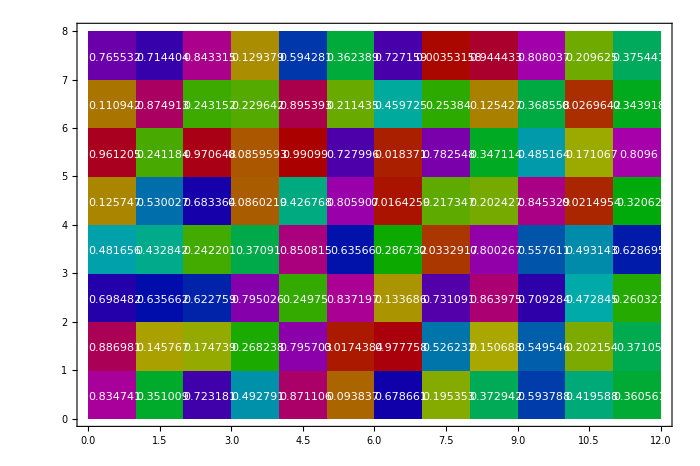

```mathematica
rl={{.5,"a"},{1.5,"b"},{2.5 ,"c"},{3.5,"d"},{4.5,"e"},{5.5, "f"},{6.5,"g"},{7.5,"h"}};
cl={{.5,"♔"},{1.5,"♕"},{2.5 ,"♖"},{3.5,"♗"},{4.5,"♘"},{5.5,"♙"},
    {6.5,"♚"},{7.5,"♛"},{8.5,"♜"},{9.5,"♝"},{10.5,"♞"},{11.5,"♟"}};
Show[MatrixPlot[m,ColorFunction->(Darker[Hue[2#]]&)],
        Table[Graphics[{White,Text[m[[j]][[i]],{i-.45,8.45-j}]}],{i,12},{j,8}],
     FrameTicks->{cl,rl},FrameTicksStyle->Medium,ImageSize->700]
```